```mathematica
(*Solving differential Eq. in mathematica*)
(* Indeterminitisc Systems(model): which can't be study by using differential eq.Bcz we can't make differentiall eq for them.*)
(*SOLVING Ordinary differential Eq. .....e.g Differential eq of SHO*)
??DSolve
```

RowBox[{"DSolve", "[", RowBox[{StyleBox["eqn", "TI"], ",", StyleBox["y", "TI"], ",", StyleBox["x", "TI"]}], "]"}] solves a differential equation for the function StyleBox["y", "TI"], with independent variable StyleBox["x", "TI"]. 
RowBox[{"DSolve", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["eqn", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["eqn", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["y", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["x", "TI"]}], "]"}] solves a list of differential equations. 
RowBox[{"DSolve", "[", RowBox[{StyleBox["eqn", "TI"], ",", StyleBox["y", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] solves a partial differential equation.

Attributes[DSolve]={Protected}
 
Options[DSolve]={GeneratedParameters→C,Method→Automatic}

```mathematica
(*DSolve : it gives us EXACT Sol.*)
```

```mathematica
(*SOLVING ODE OF SHO.*)
(*Define ODE OF SHO.*)
deq=θ''[t]+ω^2 θ[t]==0(* ω=2π/T..l=5;g=10;...  T=2π Srt(m/k) for spring mass system.  
T=2π Srt(l/g) =>   ω=Srt(g/l) for simple pendulum.  *)
(*Solve the eq Exactly/Symbolically.*)
gensol=DSolve[deq,θ[t],t]
```

ω^2 θ[t]+θ''[t]==0

{{θ[t]→C[1] Cos[t ω]+C[2] Sin[t ω]}}

```mathematica
(*Initial conds or boundary conds can be used to determine particular solution
Initial conditions:-those cond in which the value of idependent variable remains same.e.g. ,
(i)  at t=0,θ=Pi/3 and (ii) at t=0,θ'=0
second example:=at t=T/4,θ=0 and at t=T/4,θ'=max
those cond in which the idependent variable have different values,the conds are the boundary conds
*)
```

```mathematica
(*Equality operator is more prior than Assignment operator.*)
```

```mathematica
(*Extract general Solution *)
gensol=θ[t]/.gensol[[1]]
```

C[1] Cos[t ω]+C[2] Sin[t ω]

```mathematica
(*Apply initial conditions in order to Write down algebraic eq.*)
(* At right Extreme point: *)
max=Pi;
aeq1=(gensol/.t->0)==max
aeq2=(D[gensol,t]/.t->0)==0
```

C[1]==π

20 C[2]==0

```mathematica
(*Solve the algebraic eq in order to get values of arbitrary constant.*)
cons=Solve[{aeq1,aeq2},{C[1],C[2]}]
(*Put the values of constants ino general sol. in order to get Particular so. *)
θt=gensol/.cons[[1]]
vt=D[θt,t];
at=D[vt,t];
m=1;
Ke=1/2*m*vt^2;
pe=1/2*m*ω^2*θt^2;
hamiltonian=Ke+pe;
ω=20;
Plot[{θt*10,vt,at},{t,0,4*2Pi/ω},PlotStyle->{{Red,Thick},{Blue,Thick},{Green,Thick}},PlotRange->All]

Plot[{Ke,pe,hamiltonian},{t,0,4*2Pi/ω},PlotStyle->{{Red,Thick},{Blue,Thick},{Green,Thick}},PlotRange->All]
```

{{C[1]→π,C[2]→0}}

π Cos[20 t]

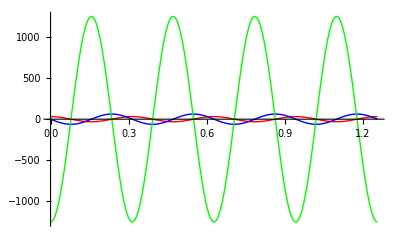

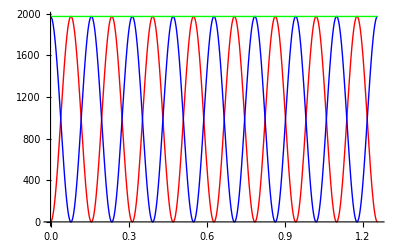

```mathematica
0
```